## Deadbeat control for an undamped, 2nd-order system with step function command signal & pulse input disturbance Example 5.10

```mathematica
Clear["Global`*"];
SetOptions[ListPlot, InterpolationOrder->0,Joined->True];
Ts=0.2;   tmax=5 Ts;
```

Design by inverse strategy so that output is a step that lags input by 1 time unit.  [not used, in the book]

OutputResponse::argt: OutputResponse called with 4 arguments; 2 or 3 arguments are expected.

OutputResponse::invsys: False is not a valid TransferFunctionModel, StateSpaceModel, AffineStateSpaceModel, or NonlinearStateSpaceModel.

OutputResponse::argt: OutputResponse called with 4 arguments; 2 or 3 arguments are expected.

OutputResponse::invsys: False is not a valid TransferFunctionModel, StateSpaceModel, AffineStateSpaceModel, or NonlinearStateSpaceModel.

OutputResponse::argt: OutputResponse called with 4 arguments; 2 or 3 arguments are expected.

General::stop: Further output of OutputResponse::argt will be suppressed during this calculation.

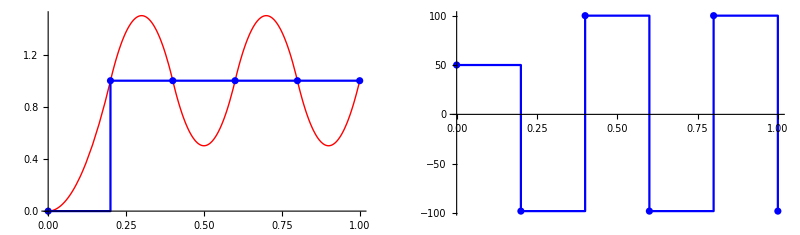

```mathematica
G0=1/(s^2+1); G0tf=TransferFunctionModel[1/(s^2+2ζ s+1),s]/.ζ->0 ; 
G0dtf=ToDiscreteTimeModel[G0tf,Ts,z,Method -> "ZeroOrderHold"];
G0d={Divide@@G0dtf[[1]]}[[1]][[1]][[1]] ;(* extract rational polynomial from tf *)
K0d=1/G0d 1/(z-1);S0d=Together[1/(1+K0d G0d)]; T0d=Together[1-S0d];KS0d=Together[K0d S0d ];  GS0d=Together[G0d S0d];

T0dtf=TransferFunctionModel[T0d,z,SamplingPeriod->Ts] ;
KS0dtf=TransferFunctionModel[KS0d,z,SamplingPeriod->Ts] ;

y0d=OutputResponse[T0dtf,UnitStep[t],{t,0,tmax}][[1]];
u0d=OutputResponse[KS0dtf,UnitStep[t],{t,0,tmax}][[1]];

datau0d=Array[{# Ts,u0d[[#]]}&,Length[u0d]];
u0dc0=Interpolation[datau0d, InterpolationOrder->0];
u0dc[t_]:=Piecewise[{{u0dc0[t],0≤t≤tmax}},0];(* convert discrete signal to continuous staircase *);
y0dc=Quiet@OutputResponse[G0tf,u0dc[t],{t,0,tmax}] (* intersample *);  

py0dc=Plot[y0dc,{t,0,tmax},PlotStyle ->{Thick,Red}];
py0d=ListPlot[y0d,DataRange->{0,tmax},Mesh->All,PlotStyle ->Blue];pu0d=ListPlot[u0d,DataRange->{0,tmax},Mesh->All,PlotStyle ->Blue];

GraphicsRow[{Show[py0dc,py0d],pu0d}]
```

```mathematica
y0d
```

OutputResponse[01100.2StateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseFalseAutomaticNone,{{Control`RecastDEquationsDump`y$38217911[t],0}},{{u_1[t],0}},Automatic,t,UnitStep[t],{t,0,1.},{}]

Forcing the system to 1 after 1 step does not work:  the velocity is not zero (and does not decay).
The real deadbeat algorithm requires two time steps:

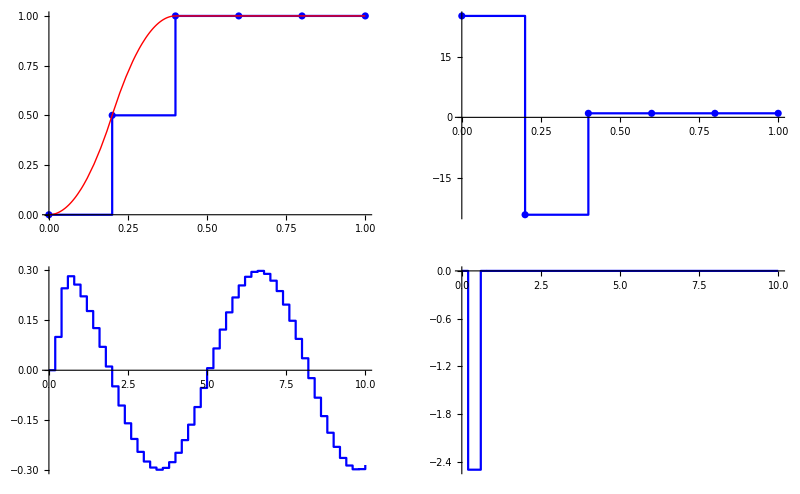

```mathematica
NumG=Numerator[G0d];  DenG=Denominator[G0d];
tmax1=5Ts;  tmax2=50 Ts; λ=NumG /.z->1;  (* λ is a scale factor *)

K1d=(DenG/(λ z^2-NumG)); S1d=Together[1/(1+K1d G0d)]; T1d=Together[1-S1d];S1dtf=TransferFunctionModel[S1d,z,SamplingPeriod->Ts] ;
T1dtf=TransferFunctionModel[T1d,z,SamplingPeriod->Ts] ;

KS1d=Together[K1d S1d]; GS1d=Together[G0d  S1d]; KS1dtf=TransferFunctionModel[KS1d,z,SamplingPeriod->Ts] ;
GS1dtf=TransferFunctionModel[GS1d,z,SamplingPeriod->Ts] ;

y1d=OutputResponse[T1dtf,UnitStep[t],{t,0,tmax1}][[1]];  (* step resp *)
u1d=OutputResponse[KS1dtf,UnitStep[t],{t,0,tmax1}][[1]]; (* control to step *)
 DiscreteImpulse=DiscreteDelta[t]/Ts;
y1ad=OutputResponse[GS1dtf,DiscreteImpulse,{t,0,tmax2}][[1]]; (* input disturb *)
u1ad=-OutputResponse[T1dtf,DiscreteImpulse,{t,0,tmax2}][[1]]; (* control sig *)

datau1d=Join[{{0,0}},Array[{# Ts,u1d[[#]]}&,Length[u1d]]];
u1dc0=Interpolation[datau1d, InterpolationOrder->0];
u1dc[t_]:=Piecewise[{{u1dc0[t],0≤t≤tmax1},{u1dc[tmax1],t>tmax1}},0];
y1dc=Quiet@OutputResponse[G0tf,u1dc[t],{t,0,tmax1}];(* intersample *)

py1dc=Plot[y1dc,{t,0,tmax1},PlotStyle ->{Thick,Red}];
py1d=ListPlot[y1d,DataRange->{0,tmax1},Mesh->All,PlotStyle->Blue];pu1d=ListPlot[u1d,DataRange->{0,tmax1},Mesh->All,PlotStyle->Blue];
py1ad=ListPlot[y1ad,DataRange->{0,tmax2},PlotStyle->Blue,PlotRange->All];
pu1ad=ListPlot[u1ad,DataRange->{0,tmax2},PlotStyle->Blue,PlotRange->All];

GraphicsGrid[{{Show[py1d,py1dc],pu1d},{py1ad,pu1ad}}]
```

```mathematica
ToDiscreteTimeModel[G0tf,Tss,z,Method -> "ZeroOrderHold"]//Simplify
```

(2 (1+z) Sin[Tss/2]^2)/(1+z^2-2 z Cos[Tss])TssTransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z11211FalseFalseFalseAutomaticNoneAutomatic

```mathematica
{G0d,K0d,GS1d,S1d,T1d}//Chop
```

{(0.0199334+0.0199334 z)/(1.-1.96013 z+z^2),(1.-1.96013 z+z^2)/((0.0199334+0.0199334 z) (-1+z)),(0.0199334 (1.+1. z) (-0.5-0.5 z+1. z^2))/(z^2 (1.-1.96013 z+z^2)),(1. (-0.5-0.5 z+1. z^2))/z^2,(0.5 (1.+1. z))/z^2}

```mathematica
K1d //Simplify
```

(1.-1.96013 z+z^2)/(-0.0199334-0.0199334 z+0.0398668 z^2)

```mathematica
G0d//Simplify
```

(0.0199334+0.0199334 z)/(1.-1.96013 z+z^2)

We can get deadbeat response after 2 time units.  BUT (see below) there is NO DAMPING to input disturbances :(

```mathematica
{zpol=z/.Solve[1.-1.9601331556824833 z+1. z^2==0,z],Abs[zpol]}
```

{{0.980067-0.198669 ⅈ,0.980067+0.198669 ⅈ},{1.,1.}}

```mathematica
{KS0dtf,KS1dtf}//Chop
```

{(50.167 (1.-1.96013 z+1. z^2))/(z (1.+1. z))0.2TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z1150.16700052984278$CellContext`z1FalseFalseFalseAutomaticNoneAutomatic,(25.0835 (1.-1.96013 z+1. z^2))/z^20.2TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z1125.083500264921111.1FalseFalseFalseAutomaticNoneAutomatic}

There is a negative pole for KS0 but not for KS1.  The former explains the ringing oscillation seen in the step response:
The input response to the command is ~ K, which means that the step, which has components at all frequencies,
excites the undamped pole at z=-1, which then always oscillates.

```mathematica
{GS0d,GS1d//Chop}
```

{(0.0199334 (-1.+z) (1.+1. z))/(z (1.-1.96013 z+z^2)),(0.0199334 (1.+1. z) (-0.5-0.5 z+1. z^2))/(z^2 (1.-1.96013 z+z^2))}

State space versions:

```mathematica
{KS0dss=StateSpaceModel[KS0dtf, SamplingPeriod->Ts],G0ss=StateSpaceModel[G0tf],T1dss=StateSpaceModel[T1dtf, SamplingPeriod->Ts]//Chop}
```

{01.00.-1.1.50.167-148.50150.1670.2StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic,010-101100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic,01.0001.0.50.500.2StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic}

```mathematica
{K1dss=StateSpaceModel[KS1dtf, SamplingPeriod->Ts]//Chop,GS1dss=StateSpaceModel[GS1dtf, SamplingPeriod->Ts]//Chop}
```

{01.0001.25.0835-49.16725.08350.2StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic,01.000001.000001.000-1.1.960131.-0.00996671-0.01993340.009966710.019933400.2StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1141FalseFalseFalseAutomaticNoneAutomatic}

## Deadbeat control, with prediction observer [omitted this part from book]

```mathematica
G0dss=ToDiscreteTimeModel[G0ss,Ts,z,Method -> "ZeroOrderHold"];
{a,b,c,d}=Normal[G0dss]  (* get a,b,c,d matrices *);
estimatorpoles={0.7,0.7}  (* sets estimator convergence rate *);
l=EstimatorGains[G0dss,estimatorpoles,Method->"Ackermann"];
deadbeatpoles={0,0}   (*  deadbeat poles are at the origin *);
k=StateFeedbackGains[G0dss,deadbeatpoles,Method->"Ackermann"];
(*k={{1,1}}; *)
```

Design the prediction  observer, with control

```mathematica
b0=ArrayFlatten[({{b}, {b}})]  (* same input for system and observer *);
c0=({{1, 0, 0, 0}, {0, 0, 1, 0}}) (* output position and estimate *); d0=ArrayFlatten[({{d}, {d}})] ;

ap0= ArrayFlatten[({{a, -b.k}, {l.c, a-b.k-l.c}})]  (* prediction observer w/ controller *);
G0pss=StateSpaceModel[{ap0,b0,c0,d0},SamplingPeriod->Ts] (* predict. obs.*);
```

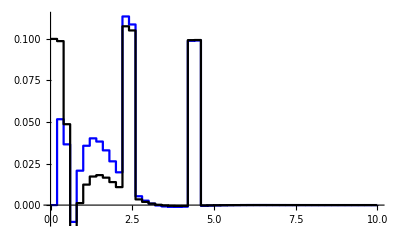

```mathematica
tmax3=50 Ts;
ic={0,0,0.1,0}   (* initial condition:  (0,0) for sys, (1,0) for observer *);DiscreteImpulse2=(DiscreteDelta[t]+DiscreteDelta[t-2]+DiscreteDelta[t-4])/Ts;
y2d=OutputResponse[{G0pss,ic},DiscreteImpulse2,{t,0,tmax3}][[1]]  (* discrete sys *);
yp2=OutputResponse[{G0pss,ic},DiscreteImpulse2,{t,0,tmax3}][[2]]  (* prediction obs *);
py2d=ListPlot[y2d,DataRange->{0,tmax3},PlotStyle ->Blue,PlotRange->All];
pyp2=ListPlot[yp2,DataRange->{0,tmax3},PlotStyle ->Black,PlotRange->All];
Show[py2d,pyp2]
```

Observer system response to an input disturbance (three pulses lasting Ts=0.2, for t = 0, 2, 4).  Since the initial condition of the observer is bad,  the observed output (blue) and the observer output, or estimate (black) differ.  After time, they reconverge, though.  At t=2, they are nearly identical and thus react more similarly, and the response dies away faster.  At t=4, they are identical and thus react identically to the input, achieving deadbeat response in 2 time steps.